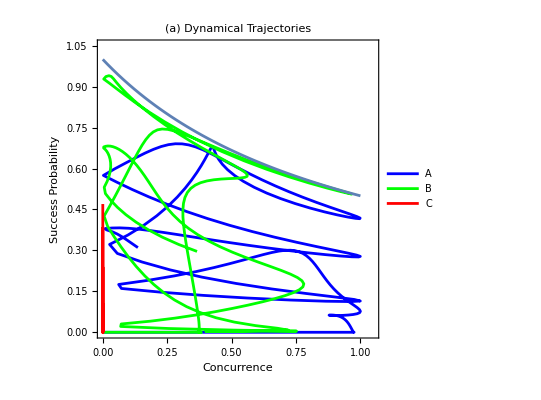

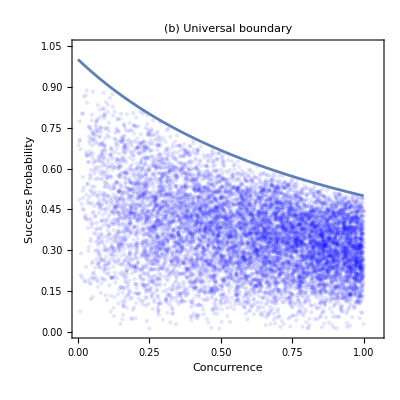

```mathematica
ClearAll["Global`*"];

PauliI=IdentityMatrix[2];
PauliX=PauliMatrix[1];
PauliY=PauliMatrix[2];
PauliZ=PauliMatrix[3];

getConcurrence[state_]:=Module[{normState,psiMatrix,sigmaY,psiTilde},normState=Normalize[state];
If[Norm[normState]==0,Return[0]];
psiMatrix=ArrayReshape[normState,{2,2}];
sigmaY=PauliY;
psiTilde=sigmaY.Conjugate[psiMatrix].sigmaY;
Abs[Conjugate[normState].Flatten[psiTilde]]];

randomSU2[]:=Module[{mat,q,r},mat=RandomComplex[{-1-I,1+I},{2,2}];
{q,r}=QRDecomposition[mat];
q/Det[q]^(1/2)];

randomSeparableState[]:=Module[{theta1,phi1,theta2,phi2,vec1,vec2},theta1=RandomReal[{0,Pi}];phi1=RandomReal[{0,2 Pi}];
theta2=RandomReal[{0,Pi}];phi2=RandomReal[{0,2 Pi}];
vec1={Cos[theta1/2],E^(I phi1) Sin[theta1/2]};
vec2={Cos[theta2/2],E^(I phi2) Sin[theta2/2]};
Flatten[Outer[Times,vec1,vec2]]];


getTrajectory[params_Association]:=Module[{omegaA,omegaB,c11X,c11Y,c11Z,c21X,c21Y,c21Z,c12X,c12Y,c12Z,c22X,c22Y,c22Z,Vq1p1,Vq2p1,Vq1p2,Vq2p2,Hinternal,Hprocess1,Hprocess2,initState,UMt,UNt,finalState,conc,pSucc},(*params*){omegaA,omegaB,c11X,c11Y,c11Z,c21X,c21Y,c21Z,c12X,c12Y,c12Z,c22X,c22Y,c22Z}=Lookup[params,{"omegaA","omegaB","c11X","c11Y","c11Z","c21X","c21Y","c21Z","c12X","c12Y","c12Z","c22X","c22Y","c22Z"},0];
initState={1,0,0,0};(*Initial states*)Vq1p1=c11X*PauliX+c11Y*PauliY+c11Z*PauliZ;
Vq2p1=c21X*PauliX+c21Y*PauliY+c21Z*PauliZ;
Vq1p2=c12X*PauliX+c12Y*PauliY+c12Z*PauliZ;
Vq2p2=c22X*PauliX+c22Y*PauliY+c22Z*PauliZ;
(*independent internal Hamiltonians*)Hinternal=KroneckerProduct[omegaA*PauliZ,PauliI]+KroneckerProduct[PauliI,omegaB*PauliZ];
Hprocess1=Hinternal+KroneckerProduct[Vq1p1,PauliI]+KroneckerProduct[PauliI,Vq2p1];
Hprocess2=Hinternal+KroneckerProduct[Vq1p2,PauliI]+KroneckerProduct[PauliI,Vq2p2];
UMt[t_]:=MatrixExp[-I*(t/2)*Hprocess1];
UNt[t_]:=MatrixExp[-I*(t/2)*Hprocess2];
finalState[t_?NumericQ]:=(UMt[t].UNt[t]-UNt[t].UMt[t]).initState;
conc[t_?NumericQ]:=getConcurrence[finalState[t]];
pSucc[t_?NumericQ]:=(1/4)*Norm[finalState[t]]^2;
Return[{conc[t],pSucc[t]}];];



paramsTraj1=<|"omegaA"->0.5,"omegaB"->0.5,"c11X"->1.5,"c22Y"->-1.2|>; 
paramsTraj2=<|"omegaA"->0.8,"omegaB"->-0.3,"c11X"->1.8,"c21Y"->0.9,"c12Z"->-1.5,"c22X"->1.1|>; 
paramsTraj3=<|"omegaA"->0,"omegaB"->0,"c11X"->-0.91,"c11Y"->-0.27,"c11Z"->0.20,"c21X"->-1.62,"c21Y"->1.75,"c21Z"->1.98,"c12X"->1.97,"c12Y"->-0.96|>; 


traj1Data=Table[getTrajectory[paramsTraj1],{t,0,10,0.05}];
traj2Data=Table[getTrajectory[paramsTraj2],{t,0,10,0.05}];
traj3Data=Table[getTrajectory[paramsTraj3],{t,0,10,0.05}];


runSingleTrialB[]:=Module[{initState,UA,UB,V1,V2,finalState,pSucc,conc},initState=randomSeparableState[];
UA=randomSU2[];
UB=randomSU2[];
V1=KroneckerProduct[UA,PauliI];
V2=KroneckerProduct[PauliI,UB];
finalState=(V1-V2).initState;
pSucc=(1/4)*Norm[finalState]^2;
conc=getConcurrence[finalState];
Return[{conc,pSucc}];];

numTrials=10000;
resultsList=Table[runSingleTrialB[],{numTrials}];

labelStyle={FontSize->14,FontFamily->"Times"};
frameStyle={FontSize->12,FontFamily->"Times"};
plotLabelStyle={FontSize->16,FontFamily->"Times",Bold};

panelA=ListLinePlot[{traj1Data,traj2Data,traj3Data},PlotRange->{{0,1.05},{0,1.05}},Frame->True,AspectRatio->1,FrameLabel->{Style["Concurrence",labelStyle],Style["Success Probability",labelStyle]},PlotLabel->Style["(a) Dynamical Trajectories",plotLabelStyle],FrameTicksStyle->frameStyle,PlotStyle->{Blue,Green,Red},PlotLegends->{"A","B","C"},Epilog->{Black,Thick,Plot[1/(1+c),{c,0,1}][[1]]},ImageSize->400];

panelB=ListPlot[resultsList,PlotRange->{{0,1.05},{0,1.05}},Frame->True,AspectRatio->1,FrameLabel->{Style["Concurrence",labelStyle],Style["Success Probability",labelStyle]},PlotLabel->Style["(b) Universal boundary",plotLabelStyle],FrameTicksStyle->frameStyle,PlotStyle->{Blue,Opacity[0.1],PointSize[Small]},Epilog->{Black,Thick,Plot[1/(1+c),{c,0,1}][[1]]},ImageSize->400];

Print[panelA];
Print[panelB];

Export["PlotA.pdf",panelA];
Export["PlotB.pdf",panelB];
```